```mathematica
Timing[

clight=2.99792458*10^8;(*Speed of light*)

(*List of simulation step number and initial velosity*)
Velo[1]={"0","6e3","1.2e4","1.8e4","2.4e4","3e4"};
Step[1]={"501","1001","1501","2001","2501","3001"};

(* Read in data file: put your directory path here *)

Table[orb[i,j]=Import["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/solenoid_scipy/result/nstep/data/alldata_amp4e-2_velo"<>ToString[Velo[1][[j]]]<>"_kene4.705e7_sleng30cm_step"<>ToString[Step[1][[i]]]<>".dat","Table"],{i,1,6},{j,1,6}];

Table[LENG[i]=Length[orb[i,1]],{i,1,6}];
Table[X[i,j]=orb[i,j][[All,1]],{i,1,6},{j,1,6}];
Table[Vx[i,j]=orb[i,j][[All,2]],{i,1,6},{j,1,6}];
Table[Y[i,j]=orb[i,j][[All,3]],{i,1,6},{j,1,6}];
Table[Vy[i,j]=orb[i,j][[All,4]],{i,1,6},{j,1,6}];
Table[Z[i,j]=orb[i,j][[All,5]],{i,1,6},{j,1,6}];
Table[Vz[i,j]=orb[i,j][[All,6]],{i,1,6},{j,1,6}];
Table[Pt[i,j]=orb[i,j][[All,7]],{i,1,6},{j,1,6}];

Table[Beta3d[i,j]=Table[{Z[i,j][[n]],(√(Vx[i,j][[n]]^2+Vy[i,j][[n]]^2+Vz[i,j][[n]]^2))/clight},{n,1,LENG[i]}],{i,1,6},{j,1,6}];

Table[PTNORM[i,j]=Table[{Z[i,j][[n]],Pt[i,j][[n]]/Pt[i,j][[1]]},{n,1,LENG[i]}],{i,1,6},{j,1,6}];

]
```

{9.951699,Null}

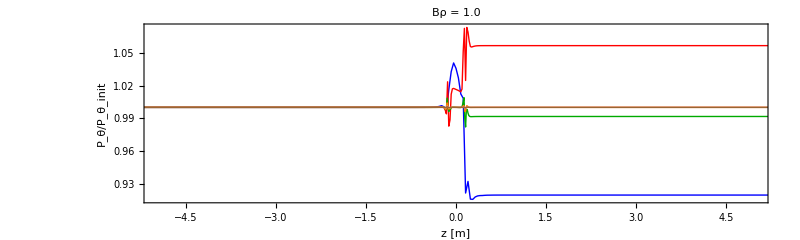

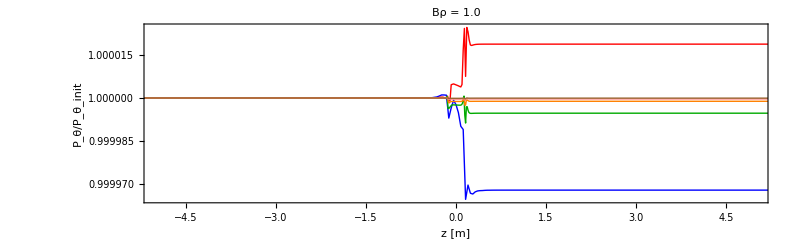

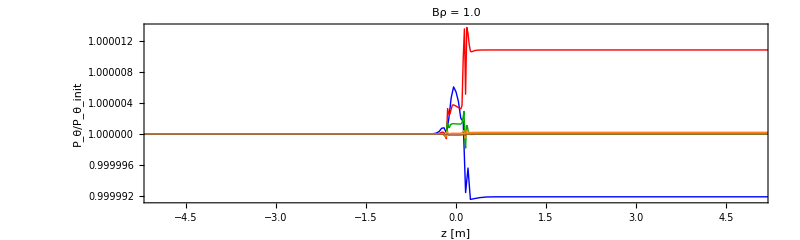

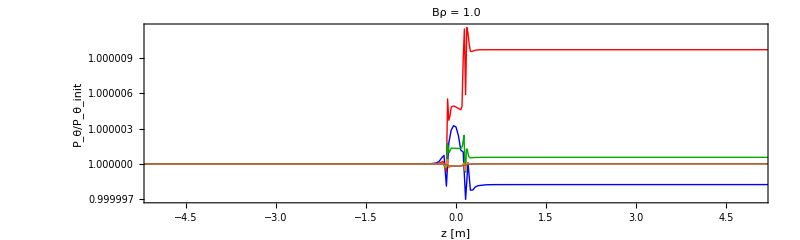

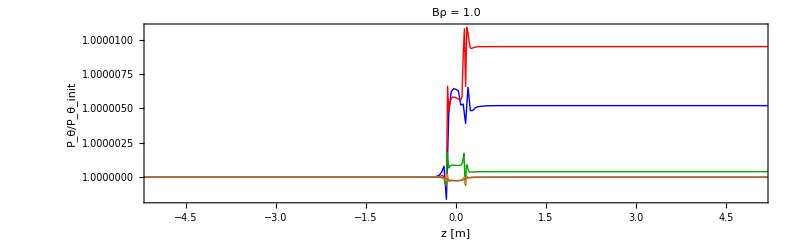

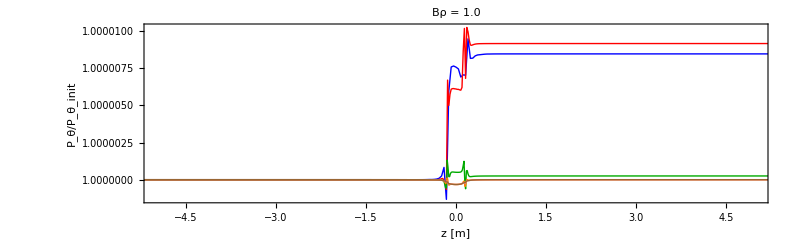

```mathematica
(*Plot of P_theta for several step size*)

PThe[1]=ListPlot[Table[PTNORM[i,1],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
PThe[2]=ListPlot[Table[PTNORM[i,2],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
PThe[3]=ListPlot[Table[PTNORM[i,3],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
PThe[4]=ListPlot[Table[PTNORM[i,4],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
PThe[5]=ListPlot[Table[PTNORM[i,5],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
PThe[6]=ListPlot[Table[PTNORM[i,6],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","P_θ/P_θ_init"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
```

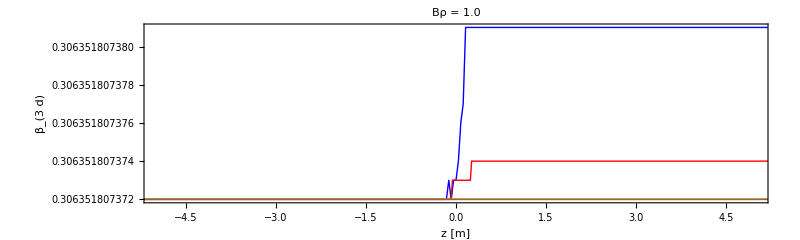

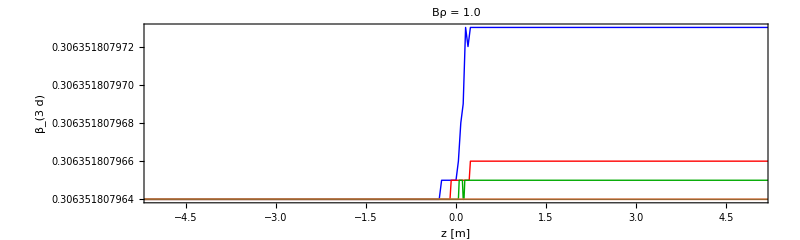

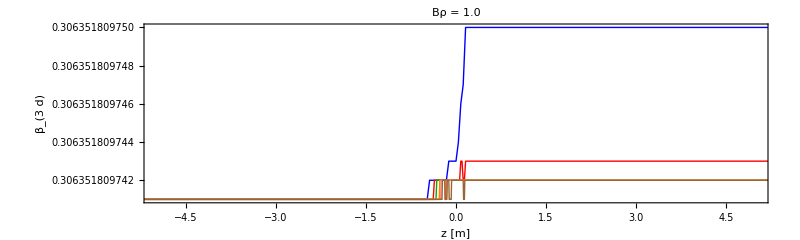

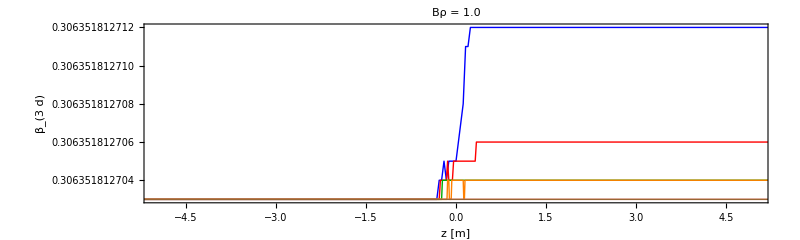

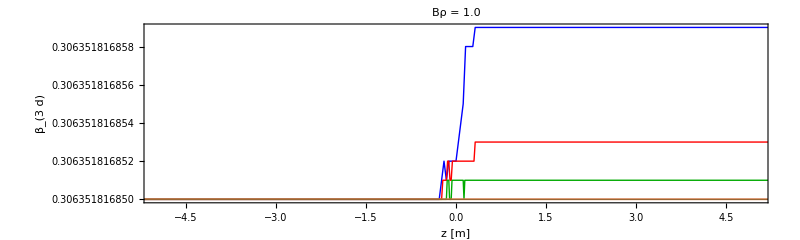

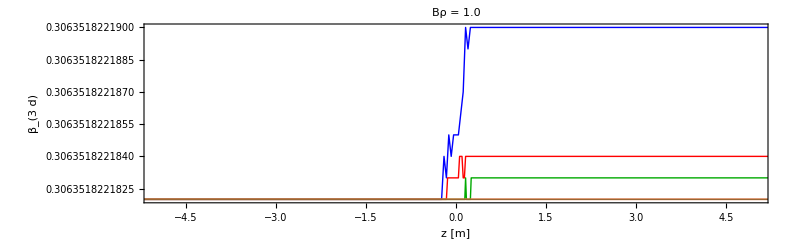

```mathematica
(*Plot of Lorentz factor beta for several step size*)

BETA[1]=ListPlot[Table[Beta3d[i,1],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","β_(3  d)"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
BETA[2]=ListPlot[Table[Beta3d[i,2],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","β_(3  d)"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
BETA[3]=ListPlot[Table[Beta3d[i,3],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","β_(3  d)"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
BETA[4]=ListPlot[Table[Beta3d[i,4],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","β_(3  d)"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
BETA[5]=ListPlot[Table[Beta3d[i,5],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","β_(3  d)"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
BETA[6]=ListPlot[Table[Beta3d[i,6],{i,1,6}],PlotRange->{{-5,5},All},Axes->None,PlotStyle->{Blue,Red,Darker[Green],Orange,Pink,Brown},AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","β_(3  d)"},LabelStyle->Directive[14],ImageSize->{800,240},PlotLabel->Style["Bρ = 1.0",15]]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/beta_velo0.eps",BETA[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/beta_velo6e3.eps",BETA[2],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/beta_velo1.2e4.eps",BETA[3],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/beta_velo1.8e4.eps",BETA[4],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/beta_velo2.4e4.eps",BETA[5],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/beta_velo3e4.eps",BETA[6],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/Ptheta_velo0.eps",PThe[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/Ptheta_velo6e3.eps",PThe[2],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/Ptheta_velo1.2e4.eps",PThe[3],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/Ptheta_velo1.8e4.eps",PThe[4],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/Ptheta_velo2.4e4.eps",PThe[5],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/nstep/Ptheta_velo3e4.eps",PThe[6],"EPS"];
```